```mathematica
import=filename↦Import[NotebookDirectory[]<>"/data-source/csse_covid_19_data/csse_covid_19_time_series/"<>filename];
confirmed=import["time_series_19-covid-Confirmed.csv"];
dead=import["time_series_19-covid-Deaths.csv"];
recovered=import["time_series_19-covid-Recovered.csv"];
stripNonValues=#[[5;;]]&;
header=confirmed[[1]];
parseShittyDate=fuckoff↦DateObject[
Map[
ToExpression,
Part[StringSplit[fuckoff,"/"],{3,1,2}]
]/.{y_,m_,d_}->{y+2000,m,d}
];
daysSince2020=Map[Composition[(#-UnixTime[{2020,1,1}])/(60 60 24)&,UnixTime,parseShittyDate],stripNonValues[header]];
onlyGerman=data↦Select[data,#[[2]]=="Germany"&][[1]];
germanConfirmed=stripNonValues[onlyGerman[confirmed]];
germanDead=stripNonValues[onlyGerman[dead]];
germanRecovered=stripNonValues[onlyGerman[recovered]];

timeSeries=data↦Transpose[{daysSince2020,data}];
dayOffsetToTick=offset↦DateString[DatePlus[DateObject["2020-01-01"],offset],{"MonthNameShort", " ","Day"}];
ticksWeekly={Table[{day,dayOffsetToTick[day]},{day,5,100,7}],Automatic};
```

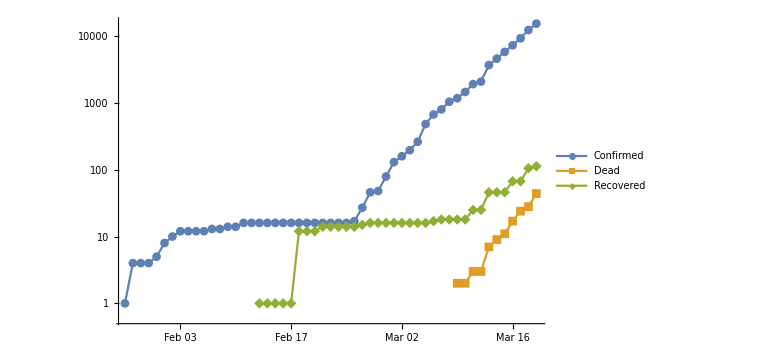

```mathematica
ListLogPlot[
timeSeries/@{germanConfirmed,germanDead,germanRecovered},
Joined->True,
PlotMarkers->Automatic,
PlotLegends->{"Confirmed","Dead","Recovered"},
ImageSize->Large,
Ticks->ticksWeekly
]
```

70734.7

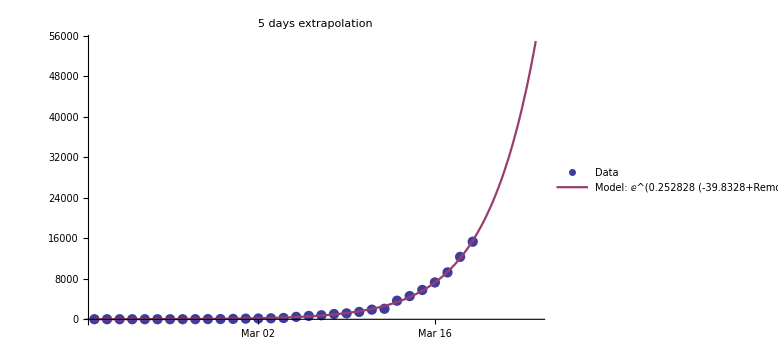
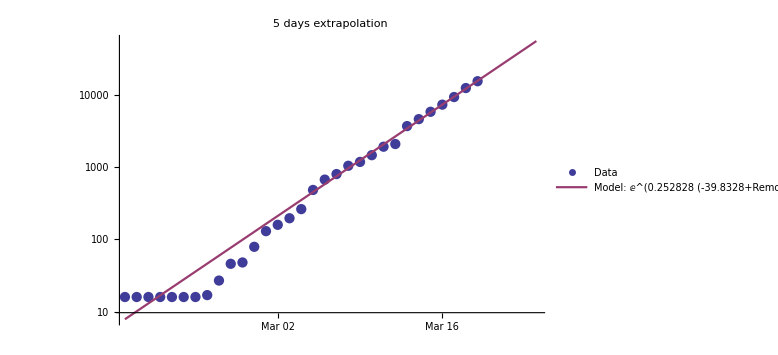
Doubling every 2.7 days
 | Estimate | Standard Error | t-Statistic | P-Value
Removed[a] | 0.252828 | 0.00315328 | 80.1794 | 1.33817×10^-35
Removed[x0] | 39.8328 | 0.457721 | 87.0244 | 1.25572×10^-36
-Graphics-
-Graphics-

```mathematica
logExtrapolation={dataInput,startDayString,daysToExtrapolate}↦Module[
{data=dataInput,nlm,timeCoordinates,mmaColors,dataPlot,modelPlot,from,to,dataLogPlot,modelLogPlot,combinedShow},

startDay=DateValue[startDayString,"ISOYearDay"];

Remove[t,a,x,x0];
data=Select[data,#/.{t_,_}->t≥startDay&];
nlm=NonlinearModelFit[data,Exp[a (x-x0)],{{a,0.3},{x0,40}},x];
timeCoordinates=Map[#/.{t_,_}->t&,data];
{from,to}={Min[timeCoordinates],Max[timeCoordinates]};

mmaColors=ColorData[1,"ColorList"];
dataPlot=ListPlot[data,PlotRange->All,PlotStyle->mmaColors[[1]],PlotLegends->{"Data"},Ticks->ticksWeekly];
modelPlot=Plot[nlm[t],{t,from,to+daysToExtrapolate},PlotRange->All,PlotStyle->mmaColors[[2]],PlotLegends->{Row@{"Model: ",Normal[nlm]}},Ticks->ticksWeekly];
dataLogPlot=ListLogPlot[data,PlotRange->All,PlotStyle->mmaColors[[1]],PlotLegends->{"Data"},Ticks->ticksWeekly];
modelLogPlot=LogPlot[nlm[t],{t,from,to+daysToExtrapolate},PlotRange->All,PlotStyle->mmaColors[[2]],PlotLegends->{Row@{"Model: ",Normal[nlm]}},Ticks->ticksWeekly];
combinedShow={d,m}↦Show[d, m,ImageSize->Large,PlotRange->All,PlotLabel->ToString[daysToExtrapolate]<>" days extrapolation"];
{
nlm,
"Doubling every "<>ToString[Round[Log[2]/(a/.nlm["BestFitParameters"]),0.1]]<>" days",
nlm["ParameterTable"],
combinedShow[dataPlot, modelPlot],
combinedShow[dataLogPlot, modelLogPlot]
}
];
result=logExtrapolation[timeSeries[germanConfirmed],"2020-02-17",5];
result/.{nlm_,__}->nlm[77+7]
result/.{_,rest__}->Column[List[rest]]
```